```mathematica
Clear["Global`*"]
Off[ClebschGordan::phy]
Off[ClebschGordan::tri]
Off[SixJSymbol::tri]
```

The Hamiltonian for two excitons on a dimer is ℋ = g μ B·(S_A+S_B) + J S_A·S_B +S_A·D_A·S_A+S_B·D_B·S_B + S_A·X·S_B

Begin by writing the one exciton spin matrices in the Zeeman basis

```mathematica
sx = 1/Sqrt[2]{{0,1,0},{1,0,1},{0,1,0}};
%//MatrixForm
sy=-ⅈ/Sqrt[2]{{0,1,0},{-1,0,1},{0,-1,0}};
%//MatrixForm
sz={{1,0,0},{0,0,0},{0,0,-1}};
%//MatrixForm
```

(0 | 1/(√2) | 0
1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0)

(0 | -ⅈ/(√2) | 0
ⅈ/(√2) | 0 | -ⅈ/(√2)
0 | ⅈ/(√2) | 0)

(1 | 0 | 0
0 | 0 | 0
0 | 0 | -1)

These matrices are ordered using states  | ++ ⟩, | 0 ⟩, | – ⟩  with quantization along the z-axis of the applied magnetic field

The 9x9 triplet pair matrix forms of the matrices is formed using Kronecker products

```mathematica
sAx=KroneckerProduct[sx,IdentityMatrix[3]];
sAy=KroneckerProduct[sy,IdentityMatrix[3]];
sAz=KroneckerProduct[sz,IdentityMatrix[3]];
sBx=KroneckerProduct[IdentityMatrix[3],sx];
sBy=KroneckerProduct[IdentityMatrix[3],sy];
sBz=KroneckerProduct[IdentityMatrix[3],sz];
```

The resulting ordering of the vectors are | + + ⟩, | + 0 ⟩, | + – ⟩, | 0 + ⟩, | 0 0 ⟩, | 0 – ⟩, | – + ⟩, | – 0 ⟩, | – – ⟩

The first term of the Hamiltonian represents interaction of the triplets with an external magnetic field B, assuming the B field points along the lab frame z-axis we have

```mathematica
(* Here we assume that the magnetic field and quantization axis points along the lab-orietnted z-axis *)
Hzeeman = Bz(sAz+sBz);
%//MatrixForm
```

(2 Bz | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Bz | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Bz | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Bz | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Bz | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Bz)

The next term in the Hamiltonian gives the isotropic exchange interaction of the two triplets

```mathematica
(* Assuming that the isotropic exchange is negative (as given by Hund's rule) and J is the absolute value *)
Hexchange = -J(sAx.sBx + sAy.sBy+sAz.sBz);
%//MatrixForm
```

(-J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0
0 | 0 | J | 0 | -J | 0 | 0 | 0 | 0
0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -J | 0 | 0 | 0 | -J | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0
0 | 0 | 0 | 0 | -J | 0 | J | 0 | 0
0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J)

For now we focus our attention on these first two terms which dominate the Hamiltonian   ℋ_0=g μ B·(S_A+S_B) + J S_A·S_B

```mathematica
(* Define Subscript[H, 0] and convert to the dimensionless quantity ϵ *)
H0 = FullSimplify[(Hzeeman+Hexchange)/J /.Bz->δ J];
%//MatrixForm
```

(-1+2 δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | δ | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | δ | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -δ | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-2 δ)

This part of the Hamiltonian is diagonal in the total spin basis, using Clebsch-Gordan coefficients we can write a unitary matrix to transform to this basis

```mathematica
UtotSpin = {{0,0,1/Sqrt[3],0,-1/Sqrt[3],0,1/Sqrt[3],0,0}, (* |0 0⟩ *)
				{0,1/Sqrt[2],0,-1/Sqrt[2],0,0,0,0,0}, (* |1 +1⟩ *)
				{0,0,1/Sqrt[2],0,0,0,-1/Sqrt[2],0,0}, (* |1 0⟩ *)
				{0,0,0,0,0,-1/Sqrt[2],0,1/Sqrt[2],0}, (* |1 -1⟩ *)
				{1,0,0,0,0,0,0,0,0}, (* |2 +2⟩ *)
				{0,1/Sqrt[2],0,1/Sqrt[2],0,0,0,0,0}, (* |2 +1⟩ *)
				{0,0,1/Sqrt[6],0,2/Sqrt[6],0,1/Sqrt[6],0,0}, (* |2 0⟩ *)
				{0,0,0,0,0,1/Sqrt[2],0,1/Sqrt[2],0}, (* |2 -1⟩ *)
				{0,0,0,0,0,0,0,0,1} (* |2 -2⟩ *)};
Transpose[%]//MatrixForm
H0TotSpin=FullSimplify[UtotSpin.H0.Transpose[UtotSpin]];
%//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
1/(√3) | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√6) | 0 | 0
0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
-1/(√3) | 0 | 0 | 0 | 0 | 0 | √(2/3) | 0 | 0
0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
1/(√3) | 0 | -1/(√2) | 0 | 0 | 0 | 1/(√6) | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1+δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1-δ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1+2 δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1+δ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-δ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-2 δ)

Plotting the energies, we have

```mathematica
plotEnergies = Simplify[Diagonal[H0TotSpin]];
legend[s_,m_]=Style[StringForm["S=``, M=``",s,m],20];
plotLegend := {legend[0,0],legend[1,+1],legend[1,0],legend[1,-1],legend[2,+2],legend[2,+1],legend[2,0],legend[2,-1],legend[2,-2]};
plotColor = {{Gray,Thick},{Darker[Green],Thick},{Blend[{Gray,Green},0.2],Thick},{Darker[Green],Dashed,Thick},{Cyan,Thick},{Blue,Thick},{Blend[{Gray,Blue},0.2],Thick},{Blue,Dashed,Thick},{Cyan,Dashed,Thick}};
pointSize=0.02;
transitionPoints = {{Red, PointSize@pointSize,Point[{1,2}]},{Red, PointSize@pointSize,Point[{1,1}]},{Red, PointSize@pointSize,Point[{1,0}]},{Red, PointSize@pointSize,Point[{2/3,1-2/3}]},{Red, PointSize@pointSize,Point[{2,1}]},{Red, PointSize@pointSize,Point[{2,-1}]}};
selectionRules = {{Red,Dashed,Line[{{1,-1},{1,0}}]}(*20->21/11*),{Red,Dashed,Line[{{2/3,-1+2/3},{2/3,1-2/3}}]}(*21->22/11*)}(*for parallel choromophores*);

export=False;
Plot[plotEnergies,{δ,0,10},PlotLabel->Style["H_0 Energy Levels",Black,28],PlotRange->{{0,2.5},{-3,3}},PlotLegends->Placed[plotLegend,{1.1,0.6}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,28],None},{Style["B_z/J",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor(*,Epilog->Join[transitionPoints,selectionRules]*)]
If[export,
Export["C:\\Users\\Sina\\Google Drive\\Research\\Singlet Fission Project\\H0_spectrum_image.png",%,ImageResolution->500],Print["Image not exported"]];
```

-Graphics-

Image not exported

Adding in now the dipole/zfs interaction...

```mathematica
(*In the principal frame of the molecule *)
(* Due to Mathematica reserved functions D -> d, E -> e, can also consider the lowercase quantities to be D/J, E/J respectively*) 
Ddipole[d_,e_] = {{-d/3 + e, 0, 0},{0,-d/3 - e,0},{0,0,2d/3}};
```

```mathematica
(*Defining active/passive rotation operators*)
Ra[angles_,actsOn_] := EulerMatrix[angles].actsOn.Transpose[EulerMatrix[angles]];
Rp[angles_,actsOn_]:=Ra[{-angles[[3]],-angles[[2]],-angles[[1]]},actsOn]
?EulerMatrix
```

Visualization of the Euler angles {α,β,γ} -> {ϕ,θ,ψ}

```mathematica
PlotEulerAngles[phi_,theta_,psi_,label_,convention_]:=Module[{xi,eta,zeta,xiprime,etaprime,zetaprime,xprime,yprime,zprime,etheta,epsi,phiarc,thetaarc,psiarc},
(* Start with z rotation *)
xi = RotationMatrix[phi,{0,0,1}].{1,0,0};
eta = RotationMatrix[phi,{0,0,1}].{0,1,0};
zeta = RotationMatrix[phi,{0,0,1}].{0,0,1};

If[convention=="x",
xiprime =RotationMatrix[theta,xi].xi;
etaprime =RotationMatrix[theta,xi].eta;
zetaprime =RotationMatrix[theta,xi].zeta;
etheta = RotationMatrix[theta/2,xi].zeta;
epsi = RotationMatrix[psi/2,zetaprime].xiprime,


(* else the convention == "y" *)
xiprime =RotationMatrix[theta,eta].xi;
etaprime =RotationMatrix[theta,eta].eta;
zetaprime =RotationMatrix[theta,eta].zeta;
etheta = RotationMatrix[theta/2,eta].zeta;
epsi = RotationMatrix[psi/2,zetaprime].etaprime;
];

xprime = RotationMatrix[psi,zetaprime].xiprime;
yprime = RotationMatrix[psi,zetaprime].etaprime;
zprime = RotationMatrix[psi,zetaprime].zetaprime;


phiarc = Table[0.7RotationMatrix[tx,{0,0,1}].{1,0,0},{tx,0,Max[phi,0.01],0.05}];

If[convention=="x",
thetaarc = Table[0.7RotationMatrix[tx,xi].zeta,{tx,0,Max[theta,0.01],0.05}];psiarc = Table[0.7RotationMatrix[tx,zetaprime].xiprime,{tx,0,Max[psi,0.01],0.05}],

(* else the convention == "y" *)
thetaarc = Table[0.7RotationMatrix[tx,eta].zeta,{tx,0,Max[theta,0.01],0.05}];
psiarc = Table[0.7RotationMatrix[tx,zetaprime].etaprime,{tx,0,Max[psi,0.01],0.05}]];

Show[
(* x,y,z axes *)
Graphics3D[{Red,Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}],
Graphics3D[{Green,Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}],
Graphics3D[{Blue,Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}],
(* e1,e2,e3 axes *)
Graphics3D[{Red,Tube[{{0,0,0},xprime},0.02],Sphere[xprime,0.1]}],
Graphics3D[{Green,Tube[{{0,0,0},yprime},0.02],Sphere[yprime,0.1]}],
Graphics3D[{Blue,Tube[{{0,0,0},zprime},0.02],Sphere[zprime,0.1]}],
(* original equator *)
Graphics3D[{Gray,Cylinder[{{0,0,-0.005},{0,0,0.005}},0.7]}],
(* new equator *)
Graphics3D[{White,Cylinder[{-0.005zprime,0.005zprime},0.7]}],
(* intersection of the two *)
Graphics3D[{Black,Tube[{{0,0,0},0.7eta}]}],
(* e1a *)
Graphics3D[{Black,Tube[{{0,0,0},0.7xi}]}],
(* ϕ angle *)
Graphics3D[{Red,Tube[phiarc,0.03]}],
(* θ angle *)
Graphics3D[{Blue,Tube[thetaarc,0.03]}],
(* ψ angle *)
Graphics3D[{Green,Tube[psiarc,0.03]}],
If[label,
Graphics3D[{
Text[Style["x",Italic,FontSize->30],{1.2,0,0}],
Text[Style["y",Italic,FontSize->30],{0,1.2,0}],
Text[Style["z",Italic,FontSize->30],{0,0,1.2}],
Text[Style["x'",Italic,FontSize->30],1.3xprime],
Text[Style["y'",Italic,FontSize->30],1.3yprime],
Text[Style["z'",Italic,FontSize->30],1.3zprime]}],{}],
Graphics3D[{
Text[Style["θ",FontSize->30],0.85 etheta],
Text[Style["ϕ",FontSize->30],{0.85Cos[phi/2],0.85Sin[phi/2],0}],
Text[Style["ψ",FontSize->30],0.85epsi]}],
PlotRange->{{-1.4,1.4},{-1.4,1.4},{-1.4,1.4}},ViewPoint->{2,2,1},ImageSize->{450,480}, SphericalRegion-> True]];
```

```mathematica
Manipulate[
PlotEulerAngles[phi,theta,psi,label,convention],
Row[{"phi (", Style["ϕ"], ")"}],
{{phi, .5, ""},0,π,.01, Appearance->"Labeled" , ImageSize-> Tiny},
Row[{"theta (", Style["θ"], ")"}],
{{theta, .8, ""},0,π,.01, Appearance->"Labeled", ImageSize-> Tiny },
Row[{"psi (", Style["ψ"], ")"}],
{{psi, 1.2, ""},0,π,.01, Appearance->"Labeled", ImageSize-> Tiny },
Delimiter,
"axes labels",
{{label,False,""},{True,False}},
"convention",
{{convention, "x", ""},{"x"-> Style["x", Italic],"y"-> Style["y", Italic]}},
SaveDefinitions->True, ControlPlacement-> Left]
```

For linked dimers we first need to rotate molecule B and molecule A into a shared ‘dimer’ frame, this corresponds to a rotation {180, -(180-β)/2,0} for molecule B and {0,-(180-β)/2,0} for molecule A, where β is the bridging angle

```mathematica
(* Switch between 'chasing' orientation of x-axes and orientation where x-axes point towards joined edge of molecules*)
chasing=False;
(*Set of angles that describes angle between B field and shared molecular axis*)
BFieldAngles={ϕ,θ,0};
(*Set of angles for molecule B that describes relation between principle frame of molecules*) 
BAngles = {If[chasing,0,Pi],If[chasing,1,-1](Pi-β)/2,0};
(* Set of angles for molecule A that describes relation between principle frame of molecules *)
AAngles ={0,-(Pi-β)/2,0};

(* Rotate from principle frame (Ddipole[d,e]) to lab frame *)
DBLab =  Rp[BFieldAngles,Ra[BAngles,Ddipole[dB,eB]]];
DBLab = FullSimplify[%];
%//MatrixForm
DALab =  Rp[BFieldAngles,Ra[AAngles,Ddipole[dA,eA]]];
DALab = FullSimplify[%];
%//MatrixForm
```

(1/24 ((-dB-3 eB+3 (dB-eB) Cos[β]) (-1+3 Cos[2 θ])+6 (dB+3 eB+(dB-eB) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+12 (-dB+eB) Cos[ϕ] Sin[β] Sin[2 θ]) | -1/2 ((dB+3 eB+(dB-eB) Cos[β]) Cos[θ] Cos[ϕ]+(-dB+eB) Sin[β] Sin[θ]) Sin[ϕ] | 1/8 ((dB-eB) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-2 (dB+3 eB) Sin[2 θ] Sin[ϕ]^2)
-1/2 ((dB+3 eB+(dB-eB) Cos[β]) Cos[θ] Cos[ϕ]+(-dB+eB) Sin[β] Sin[θ]) Sin[ϕ] | -1/12 (dB+3 eB) (1+3 Cos[2 ϕ])+1/2 (dB-eB) Cos[β] Sin[ϕ]^2 | -1/2 ((dB-eB) Cos[θ] Sin[β]+(dB+3 eB+(dB-eB) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]
1/8 ((dB-eB) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-2 (dB+3 eB) Sin[2 θ] Sin[ϕ]^2) | -1/2 ((dB-eB) Cos[θ] Sin[β]+(dB+3 eB+(dB-eB) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ] | 1/24 (-3 (dB-eB) Cos[β] (1+3 Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)+(dB+3 eB) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)+12 (dB-eB) Cos[ϕ] Sin[β] Sin[2 θ]))

(1/24 ((-dA-3 eA+3 (dA-eA) Cos[β]) (-1+3 Cos[2 θ])+6 (dA+3 eA+(dA-eA) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+12 (dA-eA) Cos[ϕ] Sin[β] Sin[2 θ]) | -1/2 ((dA+3 eA+(dA-eA) Cos[β]) Cos[θ] Cos[ϕ]+(dA-eA) Sin[β] Sin[θ]) Sin[ϕ] | 1/8 ((dA-eA) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-2 (dA+3 eA) Sin[2 θ] Sin[ϕ]^2)
-1/2 ((dA+3 eA+(dA-eA) Cos[β]) Cos[θ] Cos[ϕ]+(dA-eA) Sin[β] Sin[θ]) Sin[ϕ] | -1/12 (dA+3 eA) (1+3 Cos[2 ϕ])+1/2 (dA-eA) Cos[β] Sin[ϕ]^2 | 1/2 ((dA-eA) Cos[θ] Sin[β]-(dA+3 eA+(dA-eA) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]
1/8 ((dA-eA) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-2 (dA+3 eA) Sin[2 θ] Sin[ϕ]^2) | 1/2 ((dA-eA) Cos[θ] Sin[β]-(dA+3 eA+(dA-eA) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ] | 1/24 (-3 (dA-eA) Cos[β] (1+3 Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)+(dA+3 eA) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)+12 (-dA+eA) Cos[ϕ] Sin[β] Sin[2 θ]))

Put together the parts to form the dipole term H_dipole=S_A·D_A·S_A+S_B·D_B·S_B=Σ_αβ(S_(A,α)(D_A^(L)))_αβ S_(A, β)+S_(B,α)(D_B^(L))_αβ S_(B, β)

```mathematica
S = {sx,sy,sz};
assume = {β∈Reals,β>0,β≤Pi,ϕ∈Reals,ϕ≥ 0,ϕ≤2Pi,θ∈Reals,θ≥ 0,θ<Pi,d>e,d>0,e≥0,d∈Reals,e∈Reals};
Hdipole[ϕ_,θ_,β_] =Simplify[KroneckerProduct[Sum[Sum[DALab[[i]][[j]]*S[[i]].S[[j]],{i,1,3}],{j,1,3}],IdentityMatrix[3]] +KroneckerProduct[IdentityMatrix[3],Sum[Sum[DBLab[[i]][[j]]*S[[i]].S[[j]],{i,1,3}],{j,1,3}]]/.{dA->d,dB->d,eA->e,eB->e},Assumptions->{θ∈ Reals,ϕ∈Reals,β∈Reals,d>0,e<0}];
%//MatrixForm
```

(1/24 (-3/2 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])+(d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)) | ((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])+4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ]+24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(-d+e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | ((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | 0 | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (d-e) Cos[ϕ] Sin[β] Sin[2 θ]+24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(d-e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | 0 | 0
((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/96 (3 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])-2 (d+3 e+3 (d+3 e) Cos[2 θ]+6 (d+3 e) Cos[2 ϕ] Sin[θ]^2+36 d Cos[ϕ] Sin[β] Sin[2 θ]-36 e Cos[ϕ] Sin[β] Sin[2 θ])) | (-((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))-4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | ((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | 0 | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (d-e) Cos[ϕ] Sin[β] Sin[2 θ]+24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(d-e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | 0
1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ]-24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(-d+e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | (-((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))+4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/24 (-3/2 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])+(d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)) | 0 | 0 | ((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | 0 | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (d-e) Cos[ϕ] Sin[β] Sin[2 θ]+24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(d-e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2)
(-4 (d-e) Cos[2 θ] Cos[ϕ] Sin[β]+4 ⅈ Sin[ϕ] ((d-e) Cos[θ] Sin[β]-(d+3 e) Sin[θ] (Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]))+(d-e) Cos[β] Sin[θ] (6 Cos[θ]+Cos[θ-2 ϕ]+Cos[θ+2 ϕ]-2 ⅈ Sin[2 ϕ]))/(8 √2) | 0 | 0 | 1/96 (3 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])-2 (d+3 e+3 (d+3 e) Cos[2 θ]+6 (d+3 e) Cos[2 ϕ] Sin[θ]^2-36 d Cos[ϕ] Sin[β] Sin[2 θ]+36 e Cos[ϕ] Sin[β] Sin[2 θ])) | ((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])+4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ]+24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(-d+e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | (-((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))+4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | 0
0 | (-4 (d-e) Cos[2 θ] Cos[ϕ] Sin[β]+4 ⅈ Sin[ϕ] ((d-e) Cos[θ] Sin[β]-(d+3 e) Sin[θ] (Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]))+(d-e) Cos[β] Sin[θ] (6 Cos[θ]+Cos[θ-2 ϕ]+Cos[θ+2 ϕ]-2 ⅈ Sin[2 ϕ]))/(8 √2) | 0 | ((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/8 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])-1/12 (d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2) | (-((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))-4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | (-((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))+4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0
0 | 0 | (-4 (d-e) Cos[2 θ] Cos[ϕ] Sin[β]+4 ⅈ Sin[ϕ] ((d-e) Cos[θ] Sin[β]-(d+3 e) Sin[θ] (Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]))+(d-e) Cos[β] Sin[θ] (6 Cos[θ]+Cos[θ-2 ϕ]+Cos[θ+2 ϕ]-2 ⅈ Sin[2 ϕ]))/(8 √2) | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ]-24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(-d+e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | (-((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))+4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/96 (3 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])-2 (d+3 e+3 (d+3 e) Cos[2 θ]+6 (d+3 e) Cos[2 ϕ] Sin[θ]^2-36 d Cos[ϕ] Sin[β] Sin[2 θ]+36 e Cos[ϕ] Sin[β] Sin[2 θ])) | 0 | 0 | (-((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))+4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2)
1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (d-e) Cos[ϕ] Sin[β] Sin[2 θ]-24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(d-e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | 0 | 0 | (-((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))-4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | 0 | 1/24 (-3/2 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])+(d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)) | ((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])+4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ]+24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(-d+e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2)
0 | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (d-e) Cos[ϕ] Sin[β] Sin[2 θ]-24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(d-e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | 0 | 0 | (-((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))-4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 0 | ((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ])-4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]-2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/96 (3 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])-2 (d+3 e+3 (d+3 e) Cos[2 θ]+6 (d+3 e) Cos[2 ϕ] Sin[θ]^2+36 d Cos[ϕ] Sin[β] Sin[2 θ]-36 e Cos[ϕ] Sin[β] Sin[2 θ])) | (-((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))-4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2)
0 | 0 | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (d-e) Cos[ϕ] Sin[β] Sin[2 θ]-24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(d-e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | 0 | 0 | (-((d-e) (-4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))-4 ⅈ ((d-e) Cos[θ] Sin[β]-(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/48 ((-d-3 e+3 (d-e) Cos[β]) (-1+3 Cos[2 θ])+6 (d+3 e+(d-e) Cos[β]) Cos[θ]^2 Cos[2 ϕ]+2 (d+3 e) (1+3 Cos[2 ϕ])+12 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ]-24 ⅈ ((d+3 e+(d-e) Cos[β]) Cos[θ] Cos[ϕ]+(-d+e) Sin[β] Sin[θ]) Sin[ϕ]-12 (d-e) Cos[β] Sin[ϕ]^2) | (-((d-e) (4 Cos[2 θ] Cos[ϕ] Sin[β]+Cos[β] (3+Cos[2 ϕ]) Sin[2 θ]))+4 ⅈ ((d-e) Cos[θ] Sin[β]+(d+3 e+(d-e) Cos[β]) Cos[ϕ] Sin[θ]) Sin[ϕ]+2 (d+3 e) Sin[2 θ] Sin[ϕ]^2)/(8 √2) | 1/24 (-3/2 (d-e) Cos[β] (2+6 Cos[2 θ]+Cos[2 θ-2 ϕ]-2 Cos[2 ϕ]+Cos[2 (θ+ϕ)])+(d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)))

Alternately we can use the result of the derivation in my notes

Be aware the Mathematica uses the convention WignerD[{j,m1,m2}, ψ, θ ϕ] = e^(i m1 ψ)e^(i m2 ϕ)WignerD[{j,m1,m2},0,θ,0] which is opposite the phase of the active rotation matrix element defined in Mueller. Mathematica ALSO uses WignerD[{j,m1,m2},θ] = (d^j)_(-m1,-m2)(θ). To fix this I will define my own WignerD matrix elements

```mathematica
?Conjugate
```

```mathematica
myWignerD[{j_,m1_,m2_},ψ_,θ_,ϕ_]:=WignerD[{j,-m1,-m2},ψ,θ,ϕ]
```

```mathematica
Dtensor={e,0,Sqrt[2/3]d,0,e};
HZFS[Spinp_,Mp_,Spin_,M_]:=Sum[(-1)^w Sum[Sum[(-1)^(-Mp)Sqrt[5(2Spin+1)(2Spinp+1)]ThreeJSymbol[{2,-w},{Spin,M},{Spinp,-Mp}]SixJSymbol[{1,1,2},{Spinp,Spin,1}]Dtensor[[j+3]]myWignerD[{2,w,q},-BFieldAngles[[3]],-BFieldAngles[[2]],-BFieldAngles[[1]]]((-1)^(Spin+Spinp)myWignerD[{2,q,j},AAngles[[1]],AAngles[[2]],AAngles[[3]]]+myWignerD[{2,q,j},BAngles[[1]],BAngles[[2]],BAngles[[3]]]),{j,-2,2}],{q,-2,2}],{w,-2,2}];
HZFSKoriModified[Spinp_,Mp_,Spin_,M_]:=Sum[(-1)^q Sum[Sum[(-1)^(-Mp)Sqrt[5(2 Spin+1)(2 Spinp+1)]ThreeJSymbol[{2,q},{Spin,M},{Spinp,-Mp}]SixJSymbol[{1,1,2},{Spinp,Spin,1}]Dtensor[[qpp+3]]
myWignerD[{2,-q,qp},-BFieldAngles[[3]],-BFieldAngles[[2]],-BFieldAngles[[1]]]
((-1)^(Spin+Spinp)myWignerD[{2,qp,qpp},AAngles[[1]],AAngles[[2]],AAngles[[3]]]+myWignerD[{2,qp,qpp},BAngles[[1]],BAngles[[2]],BAngles[[3]]]),{qpp,-2,2}],{qp,-2,2}],{q,-2,2}]
HZFSMatrix=Flatten[Table[Reverse[Table[Flatten[Table[Reverse[Table[HZFS[Sp,Mp,S,M],{M,-S,S}]],{S,0,2}]],{Mp,-Sp,Sp}]],{Sp,0,2}],1];
HZFSKoriMatrix=Flatten[Table[Reverse[Table[Flatten[Table[Reverse[Table[HZFSKoriModified[Sp,Mp,S,M],{M,-S,S}]],{S,0,2}]],{Mp,-Sp,Sp}]],{Sp,0,2}],1];
```

These should give the same eigenvalues ( but not necessarily the same matrix )

```mathematica
HdipoleTotSpin=FullSimplify[UtotSpin.Hdipole[ϕ,θ,β].Transpose[UtotSpin]/.{dA->d,dB->d,eA->e,eB->e},assume];
HZFSKoriMatrix = FullSimplify[HZFSKoriMatrix,Assumptions->assume];
HZFSMatrix=FullSimplify[HZFSMatrix,Assumptions->assume];
```

```mathematica
(*HZFSMatrix//MatrixForm
HdipoleTotSpin//MatrixForm
FullSimplify[HdipoleTotSpin-HZFSMatrix]//MatrixForm
Simplify[Table[%[[i]][[j]]*Conjugate[%[[i]][[j]]],{i,1,9},{j,1,9}],Assumptions->{e∈Reals,d∈Reals,ϕ∈Reals,θ∈Reals,β∈Reals}]//MatrixForm*)
```

The full Hamiltonian is then

```mathematica
(*Assume dA, dB and eA, eB are the same (same molecule) *)
H[ϕ_,θ_,β_,δ_]=H0TotSpin+HdipoleTotSpin;
HTest[ϕ_,θ_,β_,δ_]=H0TotSpin+HZFSMatrix;
HKoriTest[ϕ_,θ_,β_,δ_]=H0TotSpin+HZFSKoriMatrix;
FullSimplify[H[0,0,β,δ]]//MatrixForm(*magnetic field along shared molecule/dimer z axis*)
```

(2 | 0 | 0 | 0 | (d+3 e+(d-e) Cos[β])/(2 √3) | 0 | (d+3 e+3 (-d+e) Cos[β])/(3 √2) | 0 | (d+3 e+(d-e) Cos[β])/(2 √3)
0 | 1+δ+1/12 (-d-3 e+3 (d-e) Cos[β]) | 0 | 1/4 (d+3 e+(d-e) Cos[β]) | 1/2 (d-e) Sin[β] | 0 | 1/2 √(3/2) (-d+e) Sin[β] | 0 | 0
0 | 0 | 1/6 (6+d+3 e+3 (-d+e) Cos[β]) | 0 | 0 | ((-d+e) Sin[β])/(2 √2) | 0 | ((-d+e) Sin[β])/(2 √2) | 0
0 | 1/4 (d+3 e+(d-e) Cos[β]) | 0 | 1-δ+1/12 (-d-3 e+3 (d-e) Cos[β]) | 0 | 0 | 1/2 √(3/2) (d-e) Sin[β] | 0 | 1/2 (-d+e) Sin[β]
(d+3 e+(d-e) Cos[β])/(2 √3) | 1/2 (d-e) Sin[β] | 0 | 0 | 1/6 (d+3 (-2+e+4 δ)+3 (-d+e) Cos[β]) | 0 | (d+3 e+(d-e) Cos[β])/(2 √6) | 0 | 0
0 | 0 | ((-d+e) Sin[β])/(2 √2) | 0 | 0 | -1+δ+1/12 (-d-3 e+3 (d-e) Cos[β]) | 0 | 1/4 (d+3 e+(d-e) Cos[β]) | 0
(d+3 e+3 (-d+e) Cos[β])/(3 √2) | 1/2 √(3/2) (-d+e) Sin[β] | 0 | 1/2 √(3/2) (d-e) Sin[β] | (d+3 e+(d-e) Cos[β])/(2 √6) | 0 | 1/6 (-d-3 (2+e)+3 (d-e) Cos[β]) | 0 | (d+3 e+(d-e) Cos[β])/(2 √6)
0 | 0 | ((-d+e) Sin[β])/(2 √2) | 0 | 0 | 1/4 (d+3 e+(d-e) Cos[β]) | 0 | -1-δ+1/12 (-d-3 e+3 (d-e) Cos[β]) | 0
(d+3 e+(d-e) Cos[β])/(2 √3) | 0 | 0 | 1/2 (-d+e) Sin[β] | 0 | 0 | (d+3 e+(d-e) Cos[β])/(2 √6) | 0 | 1/6 (d+3 (-2+e-4 δ)+3 (-d+e) Cos[β]))

```mathematica
(*Isolate the blocks to be diagonalized *)
U = {{1,0,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,1,0},
{0,1,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,0,0,1}};
%//MatrixForm
Simplify[U.HTest[ϕ,θ,β,δ].Transpose[U]]//MatrixForm
Hsimp = Simplify[(U.HTest[ϕ,θ,β,δ].Transpose[U])[[1;;4,1;;4]],Assumptions->{ϕ∈Reals,θ∈Reals,β∈Reals,δ∈Reals,δ>0,d>0,e<0}];
%//MatrixForm
eigs=FullSimplify[Eigenvalues[Hsimp/.{β->Pi/2}],Assumptions->{ϕ∈Reals,θ∈Reals,β∈Reals,δ∈Reals,δ>0,d>0,e<0}]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(2 | 0 | (ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (-1+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(8 √3) | (ⅇ^(-2 ⅈ ϕ) Cos[θ/2] ((d-e) Cos[β] (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])+Cos[θ]+6 ⅇ^(2 ⅈ ϕ) Cos[θ])+(d+3 e) (1-ⅇ^(4 ⅈ ϕ)+(-1+ⅇ^(2 ⅈ ϕ))^2 Cos[θ])) Sin[θ/2])/(2 √3) | 0 | 0 | (ⅇ^(-2 ⅈ ϕ) (ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+(d+3 e+(d-e) Cos[β]) Sin[θ/2]^4-1/2 ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[θ]^2))/(2 √3) | (ⅇ^(-2 ⅈ ϕ) (-4 ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])+12 (d+3 e+(d-e) Cos[β]) Sin[θ]^2+12 ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ]^2))/(48 √2) | (ⅇ^(-2 ⅈ ϕ) (2 (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+ⅇ^(2 ⅈ ϕ) (d+3 e-3 (d-e) Cos[β]) Sin[θ]^2))/(4 √3)
0 | 1-δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | -1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) | 3/4 (d-e) Cos[ϕ] Sin[β] Sin[2 θ] | 1/8 (-2 ⅇ^(2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4-2 ⅇ^(-2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+(-d-3 e+3 (d-e) Cos[β]) Sin[θ]^2) | (ⅇ^(-2 ⅈ ϕ) ((d+3 e+(d-e) Cos[β]) (-1+Cos[θ]+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[2 θ]))/(8 √2) | 0 | -1/2 √(3/2) (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 1/2 (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ])
(ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(8 √3) | -1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | -1+δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | 1/8 (2 ⅇ^(-2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+(d+3 e+3 (-d+e) Cos[β]) Sin[θ]^2) | 3/4 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ] | -((d-e) Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]))/(2 √2) | 1/8 ((-d-3 e+3 (d-e) Cos[β]) Sin[2 θ]+(d+3 e+(d-e) Cos[β]) Sin[θ] (2 Cos[θ] Cos[2 ϕ]+2 ⅈ Sin[2 ϕ])) | (ⅇ^(-2 ⅈ ϕ) Cos[θ/2] ((d-e) Cos[β] (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])+Cos[θ]+6 ⅇ^(2 ⅈ ϕ) Cos[θ])+(d+3 e) (1-ⅇ^(4 ⅈ ϕ)+(-1+ⅇ^(2 ⅈ ϕ))^2 Cos[θ])) Sin[θ/2])/(4 √6) | 0
(ⅇ^(-2 ⅈ ϕ) ((d+3 e+(d-e) Cos[β]) (-1+Cos[θ]+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[2 θ]))/(4 √3) | 3/4 (d-e) Cos[ϕ] Sin[β] Sin[2 θ] | 1/8 (2 ⅇ^(2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(-2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+(d+3 e+3 (-d+e) Cos[β]) Sin[θ]^2) | -1-δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | 1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) | -((d-e) Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]))/(2 √2) | 0 | (ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (-1+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(16 √6) | 1/16 ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ])
0 | 1/8 (-2 ⅇ^(-2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4-2 ⅇ^(2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+(-d-3 e+3 (d-e) Cos[β]) Sin[θ]^2) | 3/4 (-d+e) Cos[ϕ] Sin[β] Sin[2 θ] | 1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | 1+δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | (ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(16 √2) | 1/2 (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | -1/2 √(3/2) (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | 0
0 | (ⅇ^(-2 ⅈ ϕ) Cos[θ/2] ((d-e) Cos[β] (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])+Cos[θ]+6 ⅇ^(2 ⅈ ϕ) Cos[θ])+(d+3 e) (1-ⅇ^(4 ⅈ ϕ)+(-1+ⅇ^(2 ⅈ ϕ))^2 Cos[θ])) Sin[θ/2])/(4 √2) | -((d-e) Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]))/(2 √2) | -((d-e) Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]))/(2 √2) | (ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (-1+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(16 √2) | 1+1/24 (-3 (d-e) Cos[β] (1+3 Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)+(d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)) | -((d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]))/(√2) | 0 | ((d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]))/(√2)
(ⅇ^(-2 ⅈ ϕ) (2 (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+ⅇ^(2 ⅈ ϕ) (d+3 e-3 (d-e) Cos[β]) Sin[θ]^2))/(4 √3) | 0 | 1/4 ⅇ^(-2 ⅈ ϕ) Cos[θ/2] ((d-e) Cos[β] (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])+Cos[θ]+6 ⅇ^(2 ⅈ ϕ) Cos[θ])+(d+3 e) (1-ⅇ^(4 ⅈ ϕ)+(-1+ⅇ^(2 ⅈ ϕ))^2 Cos[θ])) Sin[θ/2] | 0 | 1/2 (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | -((d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]))/(√2) | -1+2 δ+1/24 (-3 (d-e) Cos[β] (1+3 Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)+(d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)) | (ⅇ^(-2 ⅈ ϕ) (2 (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+ⅇ^(2 ⅈ ϕ) (d+3 e-3 (d-e) Cos[β]) Sin[θ]^2))/(4 √6) | 0
(ⅇ^(-2 ⅈ ϕ) (-4 ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])+12 (d+3 e+(d-e) Cos[β]) Sin[θ]^2+12 ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ]^2))/(48 √2) | -1/2 √(3/2) (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | (ⅇ^(-2 ⅈ ϕ) ((d+3 e+(d-e) Cos[β]) (-1+Cos[θ]+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[2 θ]))/(8 √6) | (ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(16 √6) | -1/2 √(3/2) (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 0 | (ⅇ^(-2 ⅈ ϕ) (ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+(d+3 e+(d-e) Cos[β]) Sin[θ/2]^4-1/2 ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[θ]^2))/(2 √6) | -1+1/24 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | (ⅇ^(-2 ⅈ ϕ) (2 (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+ⅇ^(2 ⅈ ϕ) (d+3 e-3 (d-e) Cos[β]) Sin[θ]^2))/(4 √6)
(ⅇ^(-2 ⅈ ϕ) (ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+(d+3 e+(d-e) Cos[β]) Sin[θ/2]^4-1/2 ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[θ]^2))/(2 √3) | 1/2 (d-e) Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 0 | 1/16 ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (-1+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]) | 0 | ((d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]))/(√2) | 0 | (ⅇ^(-2 ⅈ ϕ) (ⅇ^(4 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+(d+3 e+(d-e) Cos[β]) Sin[θ/2]^4-1/2 ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[θ]^2))/(2 √6) | -1-2 δ+1/24 (-3 (d-e) Cos[β] (1+3 Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2)+(d+3 e) (1+3 Cos[2 θ]+6 Cos[2 ϕ] Sin[θ]^2)))

(2 | 0 | (ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (-1+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(8 √3) | (ⅇ^(-2 ⅈ ϕ) Cos[θ/2] ((d-e) Cos[β] (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])+Cos[θ]+6 ⅇ^(2 ⅈ ϕ) Cos[θ])+(d+3 e) (1-ⅇ^(4 ⅈ ϕ)+(-1+ⅇ^(2 ⅈ ϕ))^2 Cos[θ])) Sin[θ/2])/(2 √3)
0 | 1-δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | -1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) | 3/4 (d-e) Cos[ϕ] Sin[β] Sin[2 θ]
(ⅇ^(-2 ⅈ ϕ) (-2 (d+3 e+(d-e) Cos[β]) (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])) Sin[θ]+((d+3 e) (-1+2 ⅇ^(2 ⅈ ϕ))-(d-e) (1+6 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]))/(8 √3) | -1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | -1+δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | 1/8 (2 ⅇ^(-2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+(d+3 e+3 (-d+e) Cos[β]) Sin[θ]^2)
(ⅇ^(-2 ⅈ ϕ) ((d+3 e+(d-e) Cos[β]) (-1+Cos[θ]+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+ⅇ^(2 ⅈ ϕ) (-d-3 e+3 (d-e) Cos[β]) Sin[2 θ]))/(4 √3) | 3/4 (d-e) Cos[ϕ] Sin[β] Sin[2 θ] | 1/8 (2 ⅇ^(2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Cos[θ/2]^4+2 ⅇ^(-2 ⅈ ϕ) (d+3 e+(d-e) Cos[β]) Sin[θ/2]^4+(d+3 e+3 (-d+e) Cos[β]) Sin[θ]^2) | -1-δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2))

$Aborted

```mathematica
?Chop
```

```mathematica
FullSimplify[Chop[eigs[[2]]-eigs[[3]]]/.{d->0.1,e->-0.1/4,β->Pi,θ->0},Assumptions->{δ>0,δ<3,ϕ>0,ϕ<2Pi,ϕ∈Reals}]
```

1/48 ⅇ^(-4 ⅈ ϕ) (Root[1.7053×10^-13 ⅇ^(8 ⅈ ϕ)+1.45519×10^-11 ⅇ^(10 ⅈ ϕ)-1.82535×10^6 ⅇ^(12 ⅈ ϕ)+1.45519×10^-11 ⅇ^(14 ⅈ ϕ)+1.7053×10^-13 ⅇ^(16 ⅈ ϕ)+1.81899×10^-12 ⅇ^(10 ⅈ ϕ) δ+1.8883×10^6 ⅇ^(12 ⅈ ϕ) δ+1.81899×10^-12 ⅇ^(14 ⅈ ϕ) δ+1.71049×10^6 ⅇ^(12 ⅈ ϕ) δ^2-1.76947×10^6 ⅇ^(12 ⅈ ϕ) δ^3+(3.10862×10^-15 ⅇ^(4 ⅈ ϕ)-4.26326×10^-13 ⅇ^(6 ⅈ ϕ)-34306.6 ⅇ^(8 ⅈ ϕ)-4.26326×10^-13 ⅇ^(10 ⅈ ϕ)+3.10862×10^-15 ⅇ^(12 ⅈ ϕ)-8.52651×10^-14 ⅇ^(6 ⅈ ϕ) δ+76185.6 ⅇ^(8 ⅈ ϕ) δ-8.52651×10^-14 ⅇ^(10 ⅈ ϕ) δ-36864. ⅇ^(8 ⅈ ϕ) δ^2) #1+(-2.66454×10^-15 ⅇ^(2 ⅈ ϕ)+844.8 ⅇ^(4 ⅈ ϕ)-2.66454×10^-15 ⅇ^(6 ⅈ ϕ)+768. ⅇ^(4 ⅈ ϕ) δ) #1^2+16 #1^3&,2]-Root[1.7053×10^-13 ⅇ^(8 ⅈ ϕ)+1.45519×10^-11 ⅇ^(10 ⅈ ϕ)-1.82535×10^6 ⅇ^(12 ⅈ ϕ)+1.45519×10^-11 ⅇ^(14 ⅈ ϕ)+1.7053×10^-13 ⅇ^(16 ⅈ ϕ)+1.81899×10^-12 ⅇ^(10 ⅈ ϕ) δ+1.8883×10^6 ⅇ^(12 ⅈ ϕ) δ+1.81899×10^-12 ⅇ^(14 ⅈ ϕ) δ+1.71049×10^6 ⅇ^(12 ⅈ ϕ) δ^2-1.76947×10^6 ⅇ^(12 ⅈ ϕ) δ^3+(3.10862×10^-15 ⅇ^(4 ⅈ ϕ)-4.26326×10^-13 ⅇ^(6 ⅈ ϕ)-34306.6 ⅇ^(8 ⅈ ϕ)-4.26326×10^-13 ⅇ^(10 ⅈ ϕ)+3.10862×10^-15 ⅇ^(12 ⅈ ϕ)-8.52651×10^-14 ⅇ^(6 ⅈ ϕ) δ+76185.6 ⅇ^(8 ⅈ ϕ) δ-8.52651×10^-14 ⅇ^(10 ⅈ ϕ) δ-36864. ⅇ^(8 ⅈ ϕ) δ^2) #1+(-2.66454×10^-15 ⅇ^(2 ⅈ ϕ)+844.8 ⅇ^(4 ⅈ ϕ)-2.66454×10^-15 ⅇ^(6 ⅈ ϕ)+768. ⅇ^(4 ⅈ ϕ) δ) #1^2+16 #1^3&,3])

```mathematica
U.KroneckerProduct[{"|0,0⟩","|1,1⟩","|1,0⟩","|1,-1⟩","|2,2⟩","|2,1⟩","|2,0⟩","|2,-1⟩","|2,-2⟩"},{"⟨0,0|","⟨1,1|","⟨1,0|","⟨1,-1|","⟨2,2|","⟨2,1|","⟨2,0|","⟨2,-1|","⟨2,-2|"}].Transpose[U]//MatrixForm
```

(|0,0⟩ ⟨0,0| | |0,0⟩ ⟨1,-1| | |0,0⟩ ⟨2,1| | |0,0⟩ ⟨2,-1| | |0,0⟩ ⟨1,1| | |0,0⟩ ⟨1,0| | |0,0⟩ ⟨2,2| | |0,0⟩ ⟨2,0| | |0,0⟩ ⟨2,-2|
|1,-1⟩ ⟨0,0| | |1,-1⟩ ⟨1,-1| | |1,-1⟩ ⟨2,1| | |1,-1⟩ ⟨2,-1| | |1,-1⟩ ⟨1,1| | |1,-1⟩ ⟨1,0| | |1,-1⟩ ⟨2,2| | |1,-1⟩ ⟨2,0| | |1,-1⟩ ⟨2,-2|
|2,1⟩ ⟨0,0| | |2,1⟩ ⟨1,-1| | |2,1⟩ ⟨2,1| | |2,1⟩ ⟨2,-1| | |2,1⟩ ⟨1,1| | |2,1⟩ ⟨1,0| | |2,1⟩ ⟨2,2| | |2,1⟩ ⟨2,0| | |2,1⟩ ⟨2,-2|
|2,-1⟩ ⟨0,0| | |2,-1⟩ ⟨1,-1| | |2,-1⟩ ⟨2,1| | |2,-1⟩ ⟨2,-1| | |2,-1⟩ ⟨1,1| | |2,-1⟩ ⟨1,0| | |2,-1⟩ ⟨2,2| | |2,-1⟩ ⟨2,0| | |2,-1⟩ ⟨2,-2|
|1,1⟩ ⟨0,0| | |1,1⟩ ⟨1,-1| | |1,1⟩ ⟨2,1| | |1,1⟩ ⟨2,-1| | |1,1⟩ ⟨1,1| | |1,1⟩ ⟨1,0| | |1,1⟩ ⟨2,2| | |1,1⟩ ⟨2,0| | |1,1⟩ ⟨2,-2|
|1,0⟩ ⟨0,0| | |1,0⟩ ⟨1,-1| | |1,0⟩ ⟨2,1| | |1,0⟩ ⟨2,-1| | |1,0⟩ ⟨1,1| | |1,0⟩ ⟨1,0| | |1,0⟩ ⟨2,2| | |1,0⟩ ⟨2,0| | |1,0⟩ ⟨2,-2|
|2,2⟩ ⟨0,0| | |2,2⟩ ⟨1,-1| | |2,2⟩ ⟨2,1| | |2,2⟩ ⟨2,-1| | |2,2⟩ ⟨1,1| | |2,2⟩ ⟨1,0| | |2,2⟩ ⟨2,2| | |2,2⟩ ⟨2,0| | |2,2⟩ ⟨2,-2|
|2,0⟩ ⟨0,0| | |2,0⟩ ⟨1,-1| | |2,0⟩ ⟨2,1| | |2,0⟩ ⟨2,-1| | |2,0⟩ ⟨1,1| | |2,0⟩ ⟨1,0| | |2,0⟩ ⟨2,2| | |2,0⟩ ⟨2,0| | |2,0⟩ ⟨2,-2|
|2,-2⟩ ⟨0,0| | |2,-2⟩ ⟨1,-1| | |2,-2⟩ ⟨2,1| | |2,-2⟩ ⟨2,-1| | |2,-2⟩ ⟨1,1| | |2,-2⟩ ⟨1,0| | |2,-2⟩ ⟨2,2| | |2,-2⟩ ⟨2,0| | |2,-2⟩ ⟨2,-2|)

```mathematica
(* Make it easy to access different blocks of the Hamiltonian *)
blockHamiltonian ={};
vecList={"|0,0⟩","|1,1⟩","|1,0⟩","|1,-1⟩","|2,2⟩","|2,1⟩","|2,0⟩","|2,-1⟩","|2,-2⟩"};
states={};
For[i=1,i<9,i=i+1,
For[j=i+1,j<10,j=j+1,
blockHamiltonian=Append[blockHamiltonian,{{HTest[ϕ,θ,β,δ][[i]][[i]],HTest[ϕ,θ,β,δ][[i]][[j]]},{HTest[ϕ,θ,β,δ][[j]][[i]],HTest[ϕ,θ,β,δ][[j]][[j]]}}] 
]]
For[i=1;k=1,i<9,i=i+1,
For[j=i+1,j<10,j=j+1,
states=Append[states,{vecList[[i]],vecList[[j]],k}];k=k+1
]]
Transpose[states]//MatrixForm
```

(|0,0⟩ | |0,0⟩ | |0,0⟩ | |0,0⟩ | |0,0⟩ | |0,0⟩ | |0,0⟩ | |0,0⟩ | |1,1⟩ | |1,1⟩ | |1,1⟩ | |1,1⟩ | |1,1⟩ | |1,1⟩ | |1,1⟩ | |1,0⟩ | |1,0⟩ | |1,0⟩ | |1,0⟩ | |1,0⟩ | |1,0⟩ | |1,-1⟩ | |1,-1⟩ | |1,-1⟩ | |1,-1⟩ | |1,-1⟩ | |2,2⟩ | |2,2⟩ | |2,2⟩ | |2,2⟩ | |2,1⟩ | |2,1⟩ | |2,1⟩ | |2,0⟩ | |2,0⟩ | |2,-1⟩
|1,1⟩ | |1,0⟩ | |1,-1⟩ | |2,2⟩ | |2,1⟩ | |2,0⟩ | |2,-1⟩ | |2,-2⟩ | |1,0⟩ | |1,-1⟩ | |2,2⟩ | |2,1⟩ | |2,0⟩ | |2,-1⟩ | |2,-2⟩ | |1,-1⟩ | |2,2⟩ | |2,1⟩ | |2,0⟩ | |2,-1⟩ | |2,-2⟩ | |2,2⟩ | |2,1⟩ | |2,0⟩ | |2,-1⟩ | |2,-2⟩ | |2,1⟩ | |2,0⟩ | |2,-1⟩ | |2,-2⟩ | |2,0⟩ | |2,-1⟩ | |2,-2⟩ | |2,-1⟩ | |2,-2⟩ | |2,-2⟩
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36)

```mathematica
blockHamiltonian[[23]]//MatrixForm
Simplify[blockHamiltonian[[23]][[1]][[1]]-blockHamiltonian[[23]][[2]][[2]]]
```

(1-δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2) | -1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ])
-1/2 (d-e) Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | -1+δ+1/48 ((-d-3 e+3 (d-e) Cos[β]) (1+3 Cos[2 θ])-6 (d+3 e+(d-e) Cos[β]) Cos[2 ϕ] Sin[θ]^2))

2-2 δ

```mathematica
FullSimplify[blockHamiltonian[[6]]/.{β->Pi/2,ϕ->Pi/2,θ->Pi/2}]//MatrixForm
```

(2 | -1/3 √2 (d+3 e)
-1/3 √2 (d+3 e) | -1+d/3+e)

Making a plot

```mathematica
export=False;
diagEnergies[d_,e_,β_,δ_] = Diagonal[H[0,0,β,δ]];
legend[s_,m_]=Style[StringForm["S=``, M=``",s,m],20];
plotLegend = {legend[0,0],legend[1,+1],legend[1,0],legend[1,-1],legend[2,+2],legend[2,+1],legend[2,0],legend[2,-1],legend[2,-2]};
plotColor = {{Gray,Thick},{Darker[Green],Thick},{Blend[{Gray,Green},0.2],Thick},{Darker[Green],Dashed,Thick},{Cyan,Thick},{Blue,Thick},{Blend[{Gray,Blue},0.2],Thick},{Blue,Dashed,Thick},{Cyan,Dashed,Thick}};
pointSize=0.02;
transitionPoints = {{Red, PointSize@pointSize,Point[{1.46667,2}]},{Pink, PointSize@pointSize,Point[{0.1,1.06667}]},{Pink, PointSize@pointSize,Point[{3.0333,2}]},{Yellow, PointSize@pointSize,Point[{1.9,2.86667}]},{Yellow, PointSize@pointSize,Point[{2.0333,-1.06663}]},{Yellow, PointSize@pointSize,Point[{1,1.06667}]},{Yellow, PointSize@pointSize,Point[{2.1,1.06667}]},{Yellow, PointSize@pointSize,Point[{1,-0.033333}]},{Black,PointSize@pointSize,Point[{1.03333,2}]},{Black,PointSize@pointSize,Point[{0.633333,0.333337}]}};
selectionRules = {{Red,Dashed,Line[{{1,-1},{1,0}}]}(*20->21/11*),{Red,Dashed,Line[{{2/3,-1+2/3},{2/3,1-2/3}}]}(*21->22/11*)}(*for parallel choromophores*);
Plot[Evaluate[{diagEnergies[0.1,0.1/3,0,δ]}],{δ,0,10},PlotLabel->Style["",Black,28],PlotRange->{{0,3.5},{-3,3}},PlotLegends->Placed[plotLegend,{1.1,0.6}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,28],None},{Style["Bz/J",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor,Epilog->transitionPoints]
If[export,Export["C:\\Users\\Sina\\Google Drive\\Research\\Singlet Fission Project\\H_avoidedCrossingsIdentified_spectrum_image.png",%,ImageResolution->500];,Print["Image not exported"]]
```

-Graphics-

```mathematica
?Grid
```

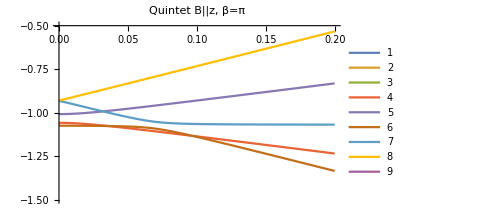
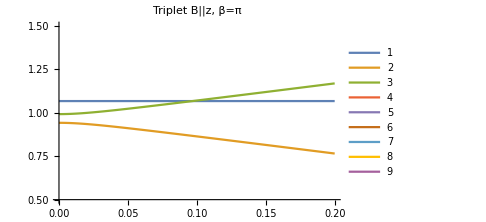
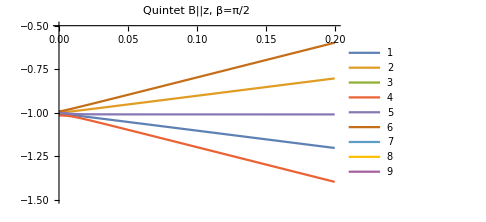
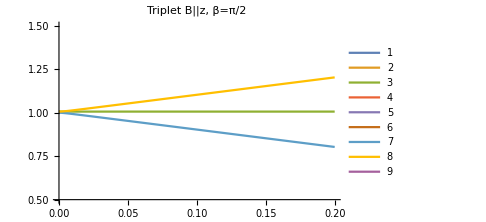
-Graphics- | -Graphics-
-Graphics- | -Graphics-

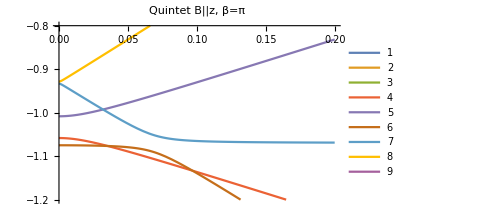
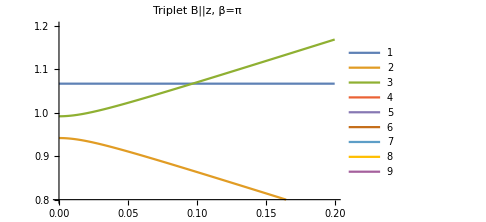
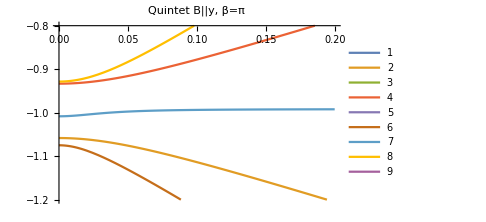
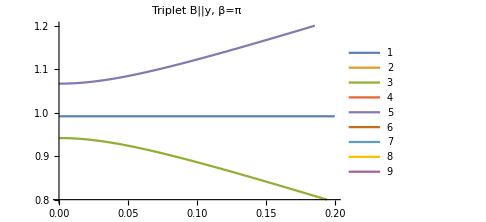
-Graphics- | -Graphics-
-Graphics- | -Graphics-

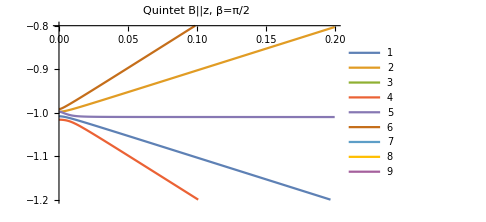
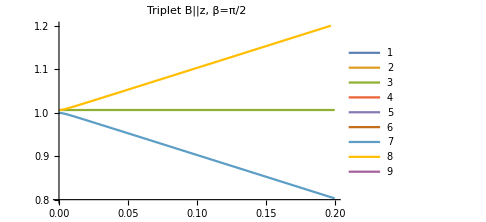
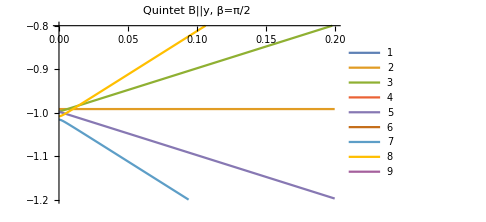
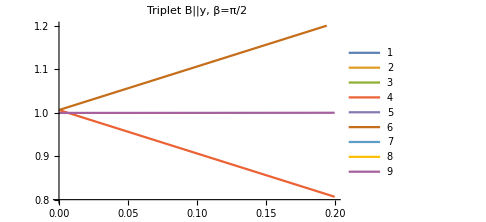
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
d=0.1;
e=-d/4;
y1=Simplify[Eigenvalues[H[0,0,Pi,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y2=Simplify[Eigenvalues[H[0,0,Pi/2,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y3=Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y4= Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi/2,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
Grid[{{Plot[Evaluate[y1],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{-1.5,-0.5}},PlotLabel->Style["Quintet B||z, β=π",Black],ImageSize->Medium],
Plot[Evaluate[y1],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{0.5,1.5}},PlotLabel->Style["Triplet B||z, β=π",Black],ImageSize->Medium]},{
Plot[Evaluate[y2],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{-1.5,-0.5}},PlotLabel->Style["Quintet B||z, β=π/2",Black],ImageSize->Medium],
Plot[Evaluate[y2],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{0.5,1.5}},PlotLabel->Style["Triplet B||z, β=π/2",Black],ImageSize->Medium]}},ItemSize->Full]
Grid[{{Plot[Evaluate[y1],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{-1.2,-0.8}},PlotLabel->Style["Quintet B||z, β=π",Black],ImageSize->Medium],
Plot[Evaluate[y1],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{0.8,1.2}},PlotLabel->Style["Triplet B||z, β=π",Black],ImageSize->Medium]},{
Plot[Evaluate[y3],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{-1.2,-0.8}},PlotLabel->Style["Quintet B||y, β=π",Black],ImageSize->Medium],
Plot[Evaluate[y3],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{0.8,1.2}},PlotLabel->Style["Triplet B||y, β=π",Black],ImageSize->Medium]}},ItemSize->Full]
Grid[{{Plot[Evaluate[y2],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{-1.2,-0.8}},PlotLabel->Style["Quintet B||z, β=π/2",Black],ImageSize->Medium],
Plot[Evaluate[y2],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{0.8,1.2}},PlotLabel->Style["Triplet B||z, β=π/2",Black],ImageSize->Medium]},{
Plot[Evaluate[y4],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{-1.2,-0.8}},PlotLabel->Style["Quintet B||y, β=π/2",Black],ImageSize->Medium],
Plot[Evaluate[y4],{δ,0,0.2},PlotLegends->Automatic,PlotRange->{{0,0.2},{0.8,1.2}},PlotLabel->Style["Triplet B||y, β=π/2",Black],ImageSize->Medium]}},ItemSize->Full](*
FullSimplify[y2[[7]]-y2[[2]]]/.δ->0
FullSimplify[y3[[3]]-y3[[4]]]/.δ->0
FullSimplify[y4[[4]]-y4[[3]]]/.δ->0*)
d=.
e=.
```

```mathematica
d=0.1;
e=-d/4;
y5=Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi/3,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y6=Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi/4,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
d=.
e=.
```

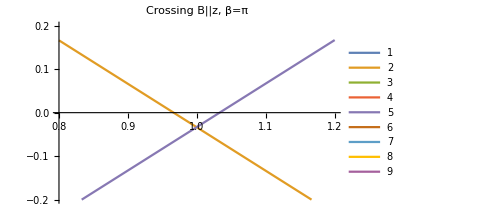
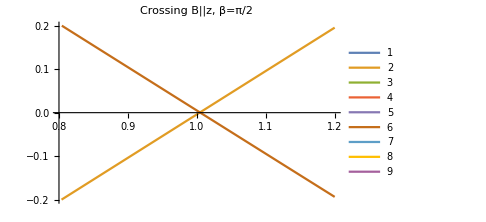
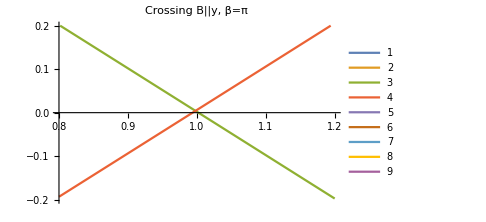
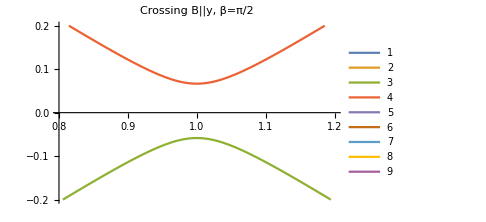
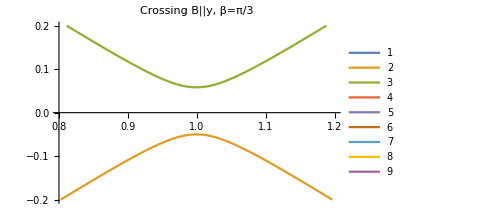
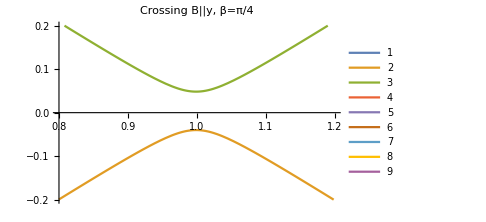
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate[y1],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||z, β=π",Black],ImageSize->Medium],
Plot[Evaluate[y2],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||z, β=π/2",Black],ImageSize->Medium],
Plot[Evaluate[y3],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π",Black],ImageSize->Medium]},{
Plot[Evaluate[y4],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π/2",Black],ImageSize->Medium],
Plot[Evaluate[y5],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π/3",Black],ImageSize->Medium],
Plot[Evaluate[y6],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π/4",Black],ImageSize->Medium]}},ItemSize->Full]
```

```mathematica
Solve[y1[[5]]==y1[[2]],δ]
FindRoot[Chop[y2[[6]]]-Chop[y2[[2]]],{δ,1}]
Solve[y3[[3]]==y3[[4]],δ]
{FindMaximum[y4[[3]],{δ,1}],FindMinimum[y4[[4]],{δ,1}]}
{FindMaximum[y5[[2]],{δ,1}],FindMinimum[y5[[3]],{δ,1}]}
{FindMaximum[y6[[2]],{δ,1}],FindMinimum[y6[[3]],{δ,1}]}
```

{{δ→-0.999687},{δ→0.999687}}

{δ→1.00453}

{{δ→-0.998045},{δ→0.998045}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{{-0.0583333,{δ→1.}},{0.0666667,{δ→1.}}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-0.0499599,{δ→0.999512}},{0.0582933,{δ→0.999512}}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-0.0400275,{δ→0.999023}},{0.0483608,{δ→0.999023}}}

```mathematica
d=0.01;
e=-d/4;
y7=Simplify[Eigenvalues[H[0,0,Pi,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y8=Simplify[Eigenvalues[H[0,0,Pi/2,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y9=Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y10=Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi/2,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y11=Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi/3,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
y12=Simplify[Eigenvalues[H[Pi/2,Pi/2,Pi/4,δ]],Assumptions->{d∈Reals, e∈Reals,d>0,e<0}];
d=.
e=.
```

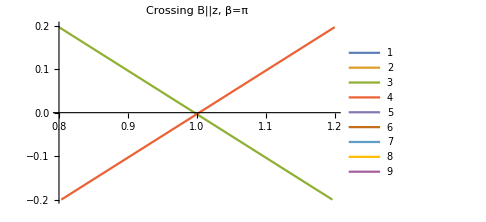
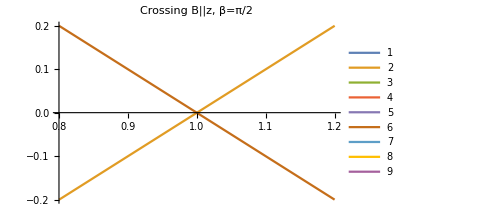
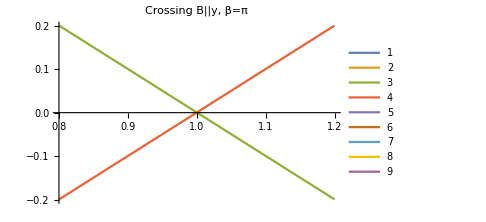
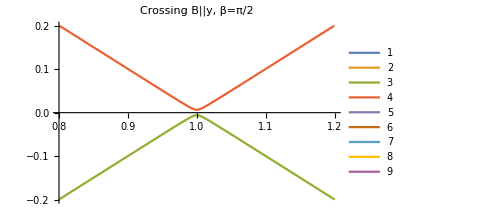
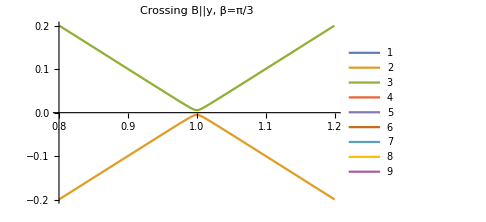
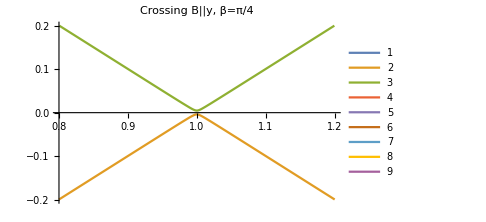
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{Plot[Evaluate[y7],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||z, β=π",Black],ImageSize->Medium],
Plot[Evaluate[y8],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||z, β=π/2",Black],ImageSize->Medium],
Plot[Evaluate[y9],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π",Black],ImageSize->Medium]},{
Plot[Evaluate[y10],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π/2",Black],ImageSize->Medium],
Plot[Evaluate[y11],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π/3",Black],ImageSize->Medium],
Plot[Evaluate[y12],{δ,0.8,1.2},PlotLegends->Automatic,PlotRange->{{0.8,1.2},{-0.2,0.2}},PlotLabel->Style["Crossing B||y, β=π/4",Black],ImageSize->Medium]}},ItemSize->Full]
```

```mathematica
Solve[y7[[3]]==y7[[4]],δ]
FindRoot[Chop[y8[[6]]]-Chop[y8[[2]]],{δ,1}]
Solve[y9[[3]]==y9[[4]],δ]
{FindMaximum[y10[[3]],{δ,1}],FindMinimum[y10[[4]],{δ,1}]}
{FindMaximum[y11[[2]],{δ,1}],FindMinimum[y11[[3]],{δ,1}]}
{FindMaximum[y12[[2]],{δ,1}],FindMinimum[y12[[3]],{δ,1}]}
```

{{δ→-0.999997},{δ→0.999997}}

{δ→1.00005}

{{δ→-0.99998},{δ→0.99998}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{{-0.00583333,{δ→1.}},{0.00666667,{δ→1.}}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-0.00499599,{δ→0.999995}},{0.00582933,{δ→0.999995}}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-0.00400275,{δ→0.99999}},{0.00483608,{δ→0.99999}}}

```mathematica
eigs=Eigenvalues[H[0,0,Pi,δ]]/.{d->0.1,e->-0.1/3};
Mapping={eigs[[9]],eigs[[5]],eigs[[1]],eigs[[3]],eigs[[8]],eigs[[4]],eigs[[7]],eigs[[2]],eigs[[6]]};
bruteforce=Plot[Mapping,{δ,0,10},PlotLabel->Style["Brute Force Method",Black,22,FontFamily->"Helvetica"],PlotRange->{{0,0.05},{-2,2.5}},PlotLegends->Placed[plotLegend,{1.1,0.6}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,18,FontFamily->"Helvetica"],None},{Style["Bz/J",Black,18,FontFamily->"Helvetica"], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor(*,Epilog->transitionPoints*)];
eigs=Eigenvalues[HTest[0,0,Pi,δ]]/.{d->0.1,e->-0.1/3};
Mapping={eigs[[9]],eigs[[5]],eigs[[1]],eigs[[3]],eigs[[8]],eigs[[4]],eigs[[7]],eigs[[2]],eigs[[6]]};
SinaTest=Plot[Mapping,{δ,0,10},PlotLabel->Style["Sina's Expression",Black,22,FontFamily->"Helvetica"],PlotRange->{{0,2},{-2,2.5}}, Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,18,FontFamily->"Helvetica"],None},{Style["Bz/J",Black,18,FontFamily->"Helvetica"], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor(*,Epilog->transitionPoints*)];
eigs=Eigenvalues[HKoriTest[0,0,Pi,δ]/.{d->0.1,e->-0.1/3}];
Mapping={eigs[[9]],eigs[[5]],eigs[[1]],eigs[[3]],eigs[[8]],eigs[[4]],eigs[[7]],eigs[[2]],eigs[[6]]};
KoriTest=Plot[Mapping,{δ,0,10},PlotLabel->Style["Kori's Expression",Black,22,FontFamily->"Helvetica"],PlotRange->{{0,2},{-2,2.5}}, Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,18,FontFamily->"Helvetica"],None},{Style["Bz/J",Black,18,FontFamily->"Helvetica"], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor(*,Epilog->transitionPoints*)];
```

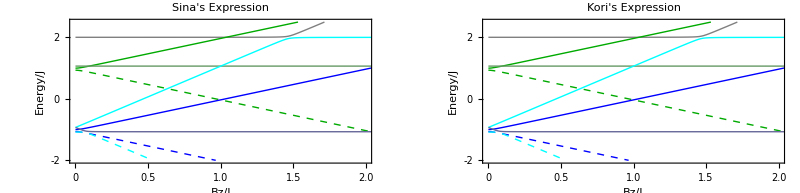

```mathematica
Show[GraphicsGrid[{{bruteforce},{SinaTest,KoriTest}},ImageSize->Full],PlotLabel->Style["Expression Comparison for β = π, B || z",Black,26,FontFamily->"Helvetica"]]
```

```mathematica
eigs=Eigenvalues[H[Pi/2,Pi/2,Pi/2,δ]]/.{d->0.1,e->-0.1/3};
Mapping={eigs[[9]],eigs[[5]],eigs[[1]],eigs[[3]],eigs[[8]],eigs[[4]],eigs[[7]],eigs[[2]],eigs[[6]]};
bruteforce=Plot[Mapping,{δ,0,10},PlotLabel->Style["Brute Force Method",Black,22,FontFamily->"Helvetica"],PlotRange->{{0,2},{-2,2.5}},PlotLegends->Placed[plotLegend,{1.1,0.6}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,18,FontFamily->"Helvetica"],None},{Style["Bz/J",Black,18,FontFamily->"Helvetica"], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor(*,Epilog->transitionPoints*)];
eigs=Eigenvalues[HTest[Pi/2,Pi/2,Pi/2,δ]]/.{d->0.1,e->-0.1/3};
Mapping={eigs[[9]],eigs[[5]],eigs[[1]],eigs[[3]],eigs[[8]],eigs[[4]],eigs[[7]],eigs[[2]],eigs[[6]]};
SinaTest=Plot[Mapping,{δ,0,10},PlotLabel->Style["Sina's Expression",Black,22,FontFamily->"Helvetica"],PlotRange->{{0,2},{-2,2.5}}, Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,18,FontFamily->"Helvetica"],None},{Style["Bz/J",Black,18,FontFamily->"Helvetica"], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor(*,Epilog->transitionPoints*)];
eigs=Eigenvalues[HKoriTest[Pi/2,Pi/2,Pi/2,δ]/.{d->0.1,e->-0.1/3}];
Mapping={eigs[[9]],eigs[[5]],eigs[[1]],eigs[[3]],eigs[[8]],eigs[[4]],eigs[[7]],eigs[[2]],eigs[[6]]};
KoriTest=Plot[Mapping,{δ,0,10},PlotLabel->Style["Kori's Expression",Black,22,FontFamily->"Helvetica"],PlotRange->{{0,2},{-2,2.5}}, Frame->{{True,False},{True,False}},FrameLabel->{{Style["Energy/J",Black,18,FontFamily->"Helvetica"],None},{Style["Bz/J",Black,18,FontFamily->"Helvetica"], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->plotColor(*,Epilog->transitionPoints*)];
```

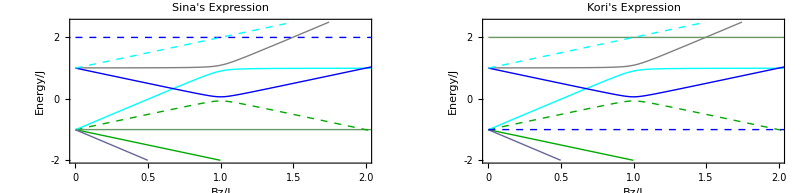

```mathematica
Show[GraphicsGrid[{{bruteforce},{SinaTest,KoriTest}},ImageSize->Full],PlotLabel->Style["Expression Comparison for β = π/2, B || y",Black,26,FontFamily->"Helvetica"]]
```

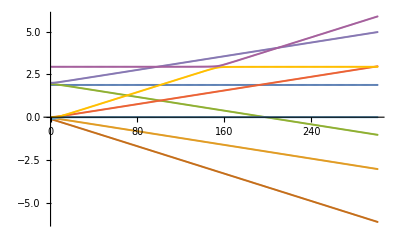

```mathematica
expression=Evaluate[Eigenvalues[HTest[0,0,0,δ]]-HTest[0,0,0,δ][[7]][[7]]]/.{d->0.1,e->-0.1/4};
parallelList=Table[expression,{δ,0,3,0.01}];
ListPlot[Transpose[%]]
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/fullSpectrum_Eigenvalues_beta180.txt",parallelList,"Table"];
```

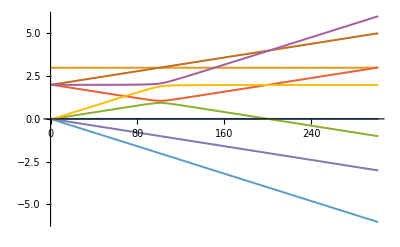

```mathematica
expression=Evaluate[Eigenvalues[HTest[Pi/2,Pi/2,Pi/2,δ]]-HTest[Pi/2,Pi/2,Pi/2,δ][[7]][[7]]]/.{d->0.1,e->-0.1/4};
bentList=Table[expression,{δ,0,3,0.01}];
ListPlot[Transpose[%]]
Export["/Users/sina/Google Drive/Research/Singlet Fission Project/fullSpectrum_Eigenvalues_beta90.txt",bentList,"Table"];
```

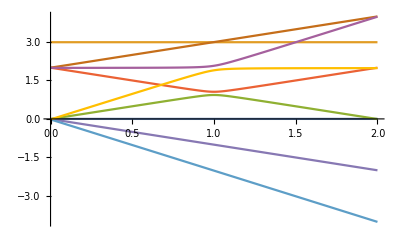

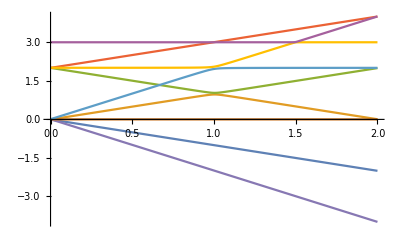

```mathematica
Plot[Evaluate[(Eigenvalues[HTest[Pi/2,Pi/2,Pi/2,δ]]-HTest[Pi/2,Pi/2,Pi/2,δ][[7]][[7]])/.{d->0.1,e->-0.1/4}],{δ,0,2}]
Plot[Evaluate[(Eigenvalues[HTest[Pi,Pi/4,Pi/2,δ]]-HTest[Pi,Pi/4,Pi/2,δ][[7]][[7]])/.{d->0.1,e->-0.1/4}],{δ,0,2}]
(*ListPlot[Transpose[%]]*)
```

```mathematica
Chop[FullSimplify[HTest[ϕ,θ,β,δ]/.{d->0.1,e->-0.1/4,δ->1}]]//MatrixForm
```

(2 | 0 | 0 | 0 | ⅇ^(2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Cos[θ/2]^4+ⅇ^(-2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Sin[θ/2]^4+(0.00360844-0.0541266 Cos[β]) Sin[θ]^2 | ⅇ^(-2 ⅈ ϕ) (0.00360844+Cos[β] (0.0180422-0.0180422 Cos[θ])+ⅇ^(4 ⅈ ϕ) (-0.00360844+Cos[β] (-0.0180422-0.0180422 Cos[θ])-0.00360844 Cos[θ])-0.00360844 Cos[θ]) Sin[θ]+(0.00360844-0.0541266 Cos[β]) Sin[2 θ] | 0.00147314+Cos[β] (-0.0220971-0.0662913 Cos[2 θ])+0.00441942 Cos[2 θ]+(0.00883883+0.0441942 Cos[β]) Cos[2 ϕ] Sin[θ]^2 | ⅇ^(-2 ⅈ ϕ) Cos[θ/2] (0.00721688+ⅇ^(4 ⅈ ϕ) (-0.00721688+Cos[β] (-0.0360844+0.0360844 Cos[θ])+0.00721688 Cos[θ])+Cos[β] (0.0360844+0.0360844 Cos[θ])+0.00721688 Cos[θ]+ⅇ^(2 ⅈ ϕ) (-0.0144338+0.216506 Cos[β]) Cos[θ]) Sin[θ/2] | ⅇ^(-2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Cos[θ/2]^4+ⅇ^(2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Sin[θ/2]^4+(0.00360844-0.0541266 Cos[β]) Sin[θ]^2
0 | 2+0.0234375 (-0.0666667+1. Cos[β]) (0.333333+1. Cos[2 θ])+(-0.003125-0.015625 Cos[β]) Cos[2 ϕ] Sin[θ]^2 | ⅇ^(-2 ⅈ ϕ) (-0.00220971+Cos[β] (-0.0110485-0.0110485 Cos[θ])+ⅇ^(4 ⅈ ϕ) (0.00220971+Cos[β] (0.0110485-0.0110485 Cos[θ])-0.00220971 Cos[θ])-0.00220971 Cos[θ]) Sin[θ]+(0.00220971-0.0331456 Cos[β]) Sin[2 θ] | 1/8 (ⅇ^(-2 ⅈ ϕ) (-0.05-0.25 Cos[β]) Cos[θ/2]^4+ⅇ^(2 ⅈ ϕ) (-0.05-0.25 Cos[β]) Sin[θ/2]^4+(-0.025+0.375 Cos[β]) Sin[θ]^2) | 0.0625 Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | -0.1875 Cos[θ] Cos[ϕ] Sin[β] Sin[θ] | -0.0765466 Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | 0.0625 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | 0
0 | ⅇ^(-2 ⅈ ϕ) (0.00220971+Cos[β] (0.0110485-0.0110485 Cos[θ])+ⅇ^(4 ⅈ ϕ) (-0.00220971+Cos[β] (-0.0110485-0.0110485 Cos[θ])-0.00220971 Cos[θ])-0.00220971 Cos[θ]) Sin[θ]+(0.00220971-0.0331456 Cos[β]) Sin[2 θ] | 1.00104+0.003125 Cos[2 θ]+0.00625 Cos[2 ϕ] Sin[θ]^2+Cos[β] (-0.015625-0.046875 Cos[2 θ]+0.03125 Cos[2 ϕ] Sin[θ]^2) | ⅇ^(-2 ⅈ ϕ) Cos[θ/2] (0.00441942+ⅇ^(4 ⅈ ϕ) (-0.00441942+Cos[β] (-0.0220971+0.0220971 Cos[θ])+0.00441942 Cos[θ])+Cos[β] (0.0220971+0.0220971 Cos[θ])+0.00441942 Cos[θ]+ⅇ^(2 ⅈ ϕ) (-0.00883883+0.132583 Cos[β]) Cos[θ]) Sin[θ/2] | -0.0883883 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) | -0.0441942 Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 0 | -0.0441942 Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | 0.0883883 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ])
0 | 1/8 (ⅇ^(2 ⅈ ϕ) (-0.05-0.25 Cos[β]) Cos[θ/2]^4+ⅇ^(-2 ⅈ ϕ) (-0.05-0.25 Cos[β]) Sin[θ/2]^4+(-0.025+0.375 Cos[β]) Sin[θ]^2) | (ⅇ^(-2 ⅈ ϕ) ((0.025+0.125 Cos[β]) (-1+Cos[θ]+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+ⅇ^(2 ⅈ ϕ) (-0.025+0.375 Cos[β]) Sin[2 θ]))/(8 √2) | 0.0234375 (-0.0666667+1. Cos[β]) (0.333333+1. Cos[2 θ])+(-0.003125-0.015625 Cos[β]) Cos[2 ϕ] Sin[θ]^2 | 0 | -0.0625 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) | -0.0765466 Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 0.1875 Cos[θ] Cos[ϕ] Sin[β] Sin[θ] | 0.0625 Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ])
ⅇ^(-2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Cos[θ/2]^4+ⅇ^(2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Sin[θ/2]^4+(0.00360844-0.0541266 Cos[β]) Sin[θ]^2 | 0.0625 Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | -0.0883883 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | 0 | 1.00104+0.003125 Cos[2 θ]+0.00625 Cos[2 ϕ] Sin[θ]^2+Cos[β] (-0.015625-0.046875 Cos[2 θ]+0.03125 Cos[2 ϕ] Sin[θ]^2) | ⅇ^(-2 ⅈ ϕ) Cos[θ/2] (0.00625+ⅇ^(4 ⅈ ϕ) (-0.00625+Cos[β] (-0.03125+0.03125 Cos[θ])+0.00625 Cos[θ])+Cos[β] (0.03125+0.03125 Cos[θ])+0.00625 Cos[θ]+ⅇ^(2 ⅈ ϕ) (-0.0125+0.1875 Cos[β]) Cos[θ]) Sin[θ/2] | ⅇ^(-2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Cos[θ/2]^4+ⅇ^(2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Sin[θ/2]^4+(0.00255155-0.0382733 Cos[β]) Sin[θ]^2 | 0 | 0
ⅇ^(-2 ⅈ ϕ) (-0.00360844+Cos[β] (-0.0180422-0.0180422 Cos[θ])+ⅇ^(4 ⅈ ϕ) (0.00360844+Cos[β] (0.0180422-0.0180422 Cos[θ])-0.00360844 Cos[θ])-0.00360844 Cos[θ]) Sin[θ]+(0.00360844-0.0541266 Cos[β]) Sin[2 θ] | -0.1875 Cos[θ] Cos[ϕ] Sin[β] Sin[θ] | -0.0441942 Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | -0.0625 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]) | 1/8 ((-0.025+0.375 Cos[β]) Sin[2 θ]+(0.025+0.125 Cos[β]) Sin[θ] (2 Cos[θ] Cos[2 ϕ]+2 ⅈ Sin[2 ϕ])) | 0.0234375 (-0.0666667+1. Cos[β]) (0.333333+1. Cos[2 θ])+(-0.003125-0.015625 Cos[β]) Cos[2 ϕ] Sin[θ]^2 | ⅇ^(-2 ⅈ ϕ) Cos[θ/2] (0.00255155+ⅇ^(4 ⅈ ϕ) (-0.00255155+Cos[β] (-0.0127578+0.0127578 Cos[θ])+0.00255155 Cos[θ])+Cos[β] (0.0127578+0.0127578 Cos[θ])+0.00255155 Cos[θ]+ⅇ^(2 ⅈ ϕ) (-0.0051031+0.0765466 Cos[β]) Cos[θ]) Sin[θ/2] | 1/8 (ⅇ^(-2 ⅈ ϕ) (0.05+0.25 Cos[β]) Cos[θ/2]^4+ⅇ^(2 ⅈ ϕ) (0.05+0.25 Cos[β]) Sin[θ/2]^4+(0.025-0.375 Cos[β]) Sin[θ]^2) | 0
0.00147314+Cos[β] (-0.0220971-0.0662913 Cos[2 θ])+0.00441942 Cos[2 θ]+(0.00883883+0.0441942 Cos[β]) Cos[2 ϕ] Sin[θ]^2 | -0.0765466 Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 0 | -0.0765466 Sin[β] (Cos[2 θ] Cos[ϕ]-ⅈ Cos[θ] Sin[ϕ]) | ⅇ^(2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Cos[θ/2]^4+ⅇ^(-2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Sin[θ/2]^4+(0.00255155-0.0382733 Cos[β]) Sin[θ]^2 | (ⅇ^(-2 ⅈ ϕ) ((0.025+0.125 Cos[β]) (-1+Cos[θ]+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+ⅇ^(2 ⅈ ϕ) (-0.025+0.375 Cos[β]) Sin[2 θ]))/(8 √6) | -1.00104-0.003125 Cos[2 θ]-0.00625 Cos[2 ϕ] Sin[θ]^2+Cos[β] (0.015625+0.046875 Cos[2 θ]-0.03125 Cos[2 ϕ] Sin[θ]^2) | ⅇ^(-2 ⅈ ϕ) (-0.00127578+Cos[β] (-0.00637888-0.00637888 Cos[θ])+ⅇ^(4 ⅈ ϕ) (0.00127578+Cos[β] (0.00637888-0.00637888 Cos[θ])-0.00127578 Cos[θ])-0.00127578 Cos[θ]) Sin[θ]+(0.00127578-0.0191366 Cos[β]) Sin[2 θ] | ⅇ^(-2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Cos[θ/2]^4+ⅇ^(2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Sin[θ/2]^4+(0.00255155-0.0382733 Cos[β]) Sin[θ]^2
(ⅇ^(-2 ⅈ ϕ) ((0.025+0.125 Cos[β]) (-1+Cos[θ]+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+ⅇ^(2 ⅈ ϕ) (-0.025+0.375 Cos[β]) Sin[2 θ]))/(4 √3) | 0.0625 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) | -0.0441942 Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 0.1875 Cos[θ] Cos[ϕ] Sin[β] Sin[θ] | 0 | 1/8 (ⅇ^(2 ⅈ ϕ) (0.05+0.25 Cos[β]) Cos[θ/2]^4+ⅇ^(-2 ⅈ ϕ) (0.05+0.25 Cos[β]) Sin[θ/2]^4+(0.025-0.375 Cos[β]) Sin[θ]^2) | ⅇ^(-2 ⅈ ϕ) (0.00127578+Cos[β] (0.00637888-0.00637888 Cos[θ])+ⅇ^(4 ⅈ ϕ) (-0.00127578+Cos[β] (-0.00637888-0.00637888 Cos[θ])-0.00127578 Cos[θ])-0.00127578 Cos[θ]) Sin[θ]+(0.00127578-0.0191366 Cos[β]) Sin[2 θ] | -2.00052-0.0015625 Cos[2 θ]-0.003125 Cos[2 ϕ] Sin[θ]^2+Cos[β] (0.0078125+0.0234375 Cos[2 θ]-0.015625 Cos[2 ϕ] Sin[θ]^2) | 1/16 ⅇ^(-2 ⅈ ϕ) (-2 (0.025+0.125 Cos[β]) (1+ⅇ^(4 ⅈ ϕ) (-1+Cos[θ])) Sin[θ]+(-0.025+0.05 ⅇ^(2 ⅈ ϕ)+(-0.125-0.75 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ])
ⅇ^(2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Cos[θ/2]^4+ⅇ^(-2 ⅈ ϕ) (0.00721688+0.0360844 Cos[β]) Sin[θ/2]^4+(0.00360844-0.0541266 Cos[β]) Sin[θ]^2 | 0 | 0.0883883 Sin[β] Sin[θ] (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) | 0.0625 Sin[β] (Cos[2 θ] Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]) | 0 | 0 | ⅇ^(2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Cos[θ/2]^4+ⅇ^(-2 ⅈ ϕ) (0.0051031+0.0255155 Cos[β]) Sin[θ/2]^4+(0.00255155-0.0382733 Cos[β]) Sin[θ]^2 | 1/16 ⅇ^(-2 ⅈ ϕ) (-2 (0.025+0.125 Cos[β]) (-1+ⅇ^(4 ⅈ ϕ) (1+Cos[θ])) Sin[θ]+(-0.025+0.05 ⅇ^(2 ⅈ ϕ)+(-0.125-0.75 ⅇ^(2 ⅈ ϕ)) Cos[β]) Sin[2 θ]) | -2.99896+0.003125 Cos[2 θ]+0.00625 Cos[2 ϕ] Sin[θ]^2+Cos[β] (-0.015625-0.046875 Cos[2 θ]+0.03125 Cos[2 ϕ] Sin[θ]^2))